```mathematica
ClearAll["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
n = 50;
```

```mathematica
randomSample = randomNumber[0,n];
```

```mathematica
sort = Sort[randomSample]
```

{1.01766,1.0343,1.49212,1.64804,1.71142,1.93966,2.32344,2.55346,2.5538,2.574,2.62304,2.66631,2.9859,3.18355,3.26431,3.32971,3.58578,3.77521,3.98872,4.02015,4.06761,4.07198,4.24674,4.35474,4.36772,4.45131,4.48869,4.71154,4.71565,4.77912,4.88237,5.07755,5.38593,5.89989,6.01744,6.20962,6.24864,6.31029,6.52281,6.69153,6.95075,7.23734,7.72124,7.72674,8.3698,8.88477,9.09875,9.46158,9.96006,12.5211}

```mathematica
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
cdf = Transpose[{sort, pdata}];
```

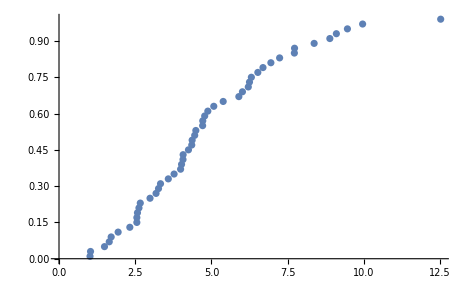

```mathematica
ListPlot[cdf]
```

```mathematica
μ = Mean[sort]
```

4.87408

```mathematica
s = StandardDeviation[sort]
```

2.52767

```mathematica
solA = NSolve[Integrate[x*E^(-a*x), {x, 0, ∞}] == μ, a][[1]][[1]][[2]]
```

0.452954

```mathematica
solA
```

0.452954

```mathematica
solA2 =NSolve[Integrate[x*x*E^(-a*x), {x, 0, ∞}] == μ, a, Reals][[1]][[1]][[2]]
```

0.743098

```mathematica
pdf1[x_] := E^(-solA*x)
```

```mathematica
pdf2[x_] = x*E^(-solA2*x)
```

ⅇ^(-0.743098 x) x

```mathematica
pdf3[x_] := x*(x+0)*E^(-0*x)
```

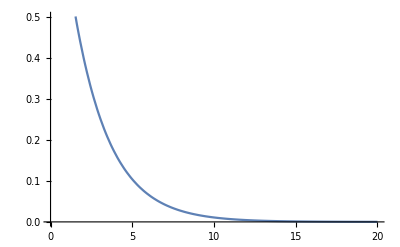

```mathematica
Show[Plot[pdf1[x], {x, 0, 20}]]
```

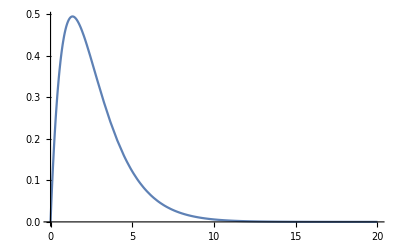

```mathematica
Plot[pdf2[x], {x, 0, 20}]
```

```mathematica
(*NSolve[{Integrate[x^2 * x*(x+b)*E^(-a*x) - (x*x*(x+b)*E^(-a*x))^2, {x, 0, n}]== s^2, Integrate[(x+b)*x*x*E^(-a*x), {x, 0, n}] == μ}, {a,b}]*)
```

```mathematica
listFun1[x_] := pdf1[sort[[x]]]
```

```mathematica
modelList1 = Array[listFun1, n];
```

```mathematica
comparedata1 = Transpose[{modelList1,pdata}];
```

```mathematica
dataplot1=ListPlot[comparedata1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf", PlotRange->{0, 1}];
```

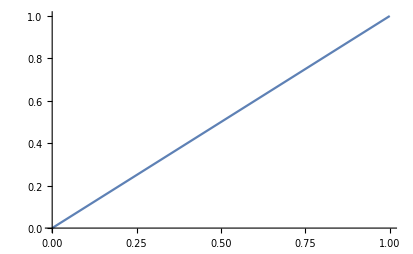

```mathematica
lineplot =Plot[x, {x, 0, 1}]
```

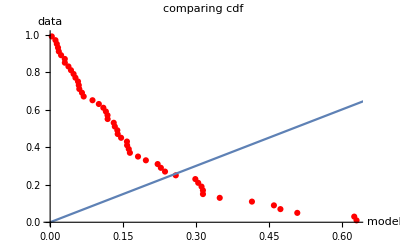

```mathematica
Show[dataplot1,lineplot]
```

```mathematica
listFun2[x_] := pdf2[sort[[x]]]
```

```mathematica
modelList2= Array[listFun2, n];
```

```mathematica
comparedata2 = Transpose[{modelList2,pdata}];
```

```mathematica
dataplot2=ListPlot[comparedata2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf", PlotRange->{0, 1}];
```

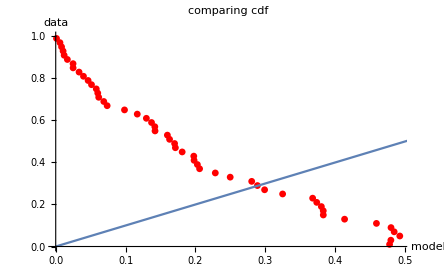

```mathematica
Show[dataplot2,lineplot]
```

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

First distribution------------------------------------------------------------------------------------------

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[1, n];
FindDistribution[numbers]
```

ExponentialDistribution[4.40563]

```mathematica
μ = Mean[numbers];
```

```mathematica
σ = StandardDeviation[numbers];
```

```mathematica
distribution = EstimatedDistribution[numbers, ExponentialDistribution[1/μ]];
```

```mathematica
cdf = CDF[distribution, numbers];
```

```mathematica
propPlot = ProbabilityPlot[numbers, distribution];
```

```mathematica
linePlot = Plot[x, {x, 0, 1}];
```

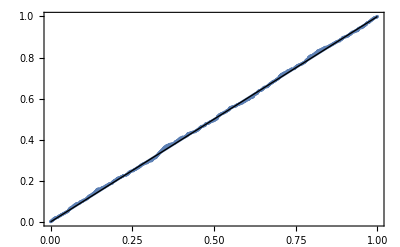

```mathematica
Show[propPlot, linePlot]
```

Andra saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[2, n];
FindDistribution[numbers]
```

GeometricDistribution[0.0654022]

```mathematica
sort = Sort[numbers];
```

```mathematica
distribution=EstimatedDistribution[numbers,GeometricDistribution[p]]
```

GeometricDistribution[0.0654022]

```mathematica
cdf = CDF[distribution, sort];
```

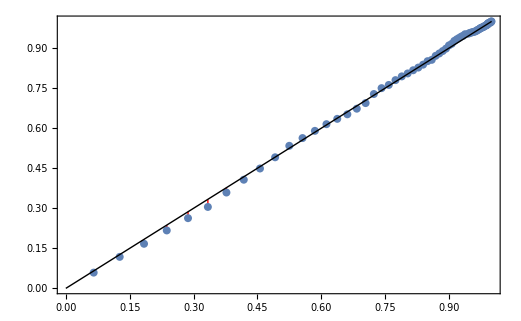

```mathematica
probPlot = ProbabilityPlot[numbers, distribution, Filling->Automatic,FillingStyle->Red]
```

```mathematica
linePlot = Plot[x, {x, 0, 1}];
```

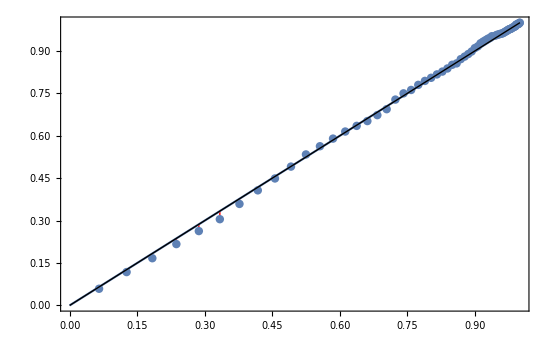

```mathematica
Show[probPlot, linePlot]
```

Tredje saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[3, n];
FindDistribution[numbers]
```

GammaDistribution[8.1645,1.55737]

```mathematica
distribution=EstimatedDistribution[numbers,GammaDistribution[α,β]]
```

GammaDistribution[8.06398,1.56935]

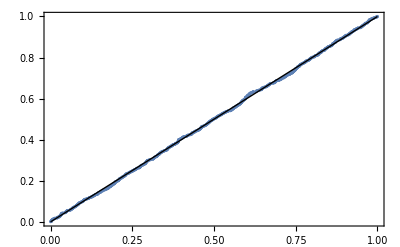

```mathematica
ProbabilityPlot[numbers, distribution]
```

Fjärde saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[4, n];
FindDistribution[numbers]
```

NormalDistribution[3.11516,4.8951]

```mathematica
μ = Mean[numbers];
```

```mathematica
σ = StandardDeviation[numbers];
```

```mathematica
distribution=EstimatedDistribution[numbers, NormalDistribution[μ,σ]]
```

NormalDistribution[3.11516,4.89755]

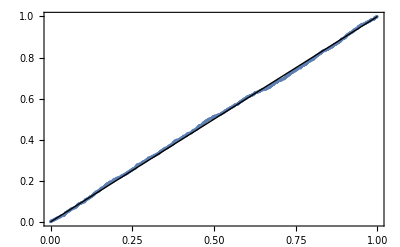

```mathematica
ProbabilityPlot[numbers, distribution]
```

Femte saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[5, n];
FindDistribution[numbers]
```

BinomialDistribution[12,0.282285]

```mathematica
distribution = EstimatedDistribution[numbers, BinomialDistribution[n, p]]
```

BinomialDistribution[1000,0.003328]

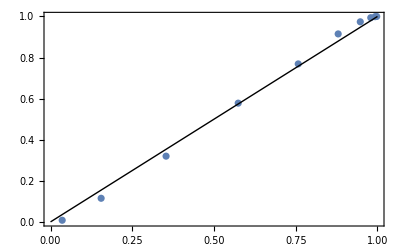

```mathematica
ProbabilityPlot[numbers, distribution]
```

Sjätte saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[6, n];
FindDistribution[numbers]
```

PoissonDistribution[9.795]

```mathematica
μ=Mean[numbers];
```

```mathematica
distribution = EstimatedDistribution[numbers, PoissonDistribution[μ]];
```

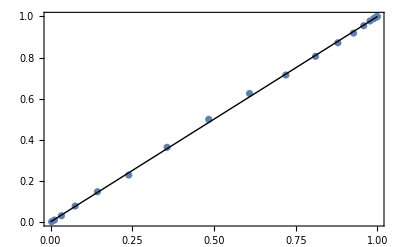

```mathematica
ProbabilityPlot[numbers, distribution]
```